```mathematica
tcheby[npts_,xmin_,xmax_]:=Module[{pts,fb,del},del=xmax-xmin;pts=N[Table[(i del)/(npts+1)+xmin,{i,npts}]];fbrke=N[Table[((i π)/del)^2,{i,npts}]];w=N[Table[del/(npts+1),{i,npts}]];T=N[Table[√(2./(npts+1)) Sin[((i j) π)/(npts+1)],{i,npts},{j,npts}]];Return[{pts,T,fbrke,w}]]
dv2fb[DVR_,T_]:=T.DVR.Transpose[T];
fb2dv[FBR_,T_]:=Transpose[T].FBR.T;
```

```mathematica
npts = 100 ; 
xmin = -3.0;
xmax = +32.0;
De = 3.0;
a = .5 ; 
m = 1.0; 
ℏ  = 1.0; 
{pts,T,fbrke,w} = tcheby[npts,xmin,xmax];
V[x_]:= De ( 1- Exp[- a x])^2-De;
Vdvr = V[pts]//Thread;
fbrke = fbrke * ℏ^2/(2m);
Hdvr =  fb2dv[DiagonalMatrix[fbrke],T] + DiagonalMatrix[Vdvr];
```

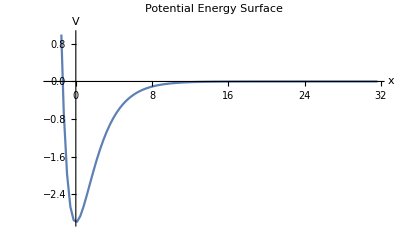

```mathematica
plotV=ListPlot[Transpose[{pts,Vdvr}],PlotRange->{-3,1},Joined->True,AxesLabel->{"x","V"},PlotLabel->"Potential Energy Surface"]
```

```mathematica
{ω,ϕ}=Transpose[Sort[Transpose[Eigensystem[Hdvr]]]];
```

```mathematica
TableForm[Take[ω,10]]
```

-2.41888
-1.44413
-0.719388
-0.244643
-0.0198923
0.0113421
0.0400867
0.0823905
0.136925
0.202919

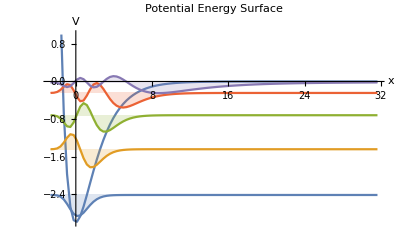

```mathematica
pltWF = ListPlot[Table[Transpose[{pts,ω[[i]]+ϕ[[i]]}],{i,1,5}],PlotRange->{{-3,32},{-3,1}},Joined->True,
Filling->Table[i->ω[[i]],{i,1,5}]];
Show[plotV,pltWF]
```

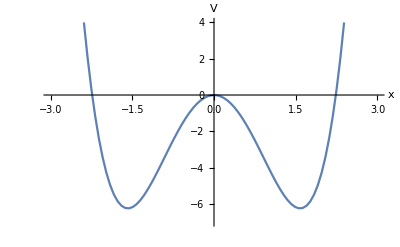

```mathematica
{pts2,T2,fbrke2,w2}=tcheby[100,-3.5,3.5];
V2[x_]:=-5 x^2+x^4;
Vdvr2=Thread[V2[pts2]];
m=1.;
pltV = ListPlot[Transpose[{pts2,Vdvr2}],PlotRange->{{-3,3},{-7,4}},Joined->True,AxesLabel->{"x","V"}]
fbrke2=fbrke2/(2 m);Hdvr=fb2dv[DiagonalMatrix[fbrke2],T2]+DiagonalMatrix[Vdvr2];{ω,ψ}=Transpose[Sort[Transpose[Eigensystem[Hdvr]]]];
```

```mathematica
TableForm[Take[ω,10]]
```

-4.13576
-4.11911
-0.756761
-0.210676
1.92129
3.8373
6.18057
8.7403
11.5102
14.4645

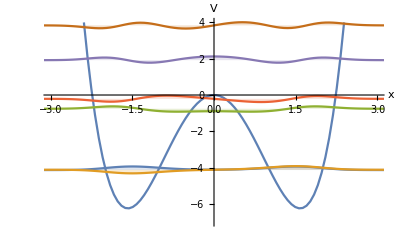

```mathematica
nn = 10;
pltWF = ListPlot[Table[Transpose[{pts2,ω[[i]]+ψ[[i]]}],{i,1,nn}],Joined->True,
Filling->Table[i->ω[[i]],{i,1,nn}]];
Show[pltV,pltWF]
```

```mathematica
npts = 25;
xmin = -3.5;
xmax = 3.5;
params = {A-> 1,B-> -5,xo-> 1.5,β-> 0.5,ℏ-> 1,δt-> 0.1,m-> 1};

V[x_]:=-5 x^2+x^4;

tcheby[npts_,xmin_,xmax_]:=Module[{pts,fb,del},del=xmax-xmin;
pts=Table[i*del*(1/(npts+1))+xmin,{i,npts}]//N;
fbrke=Table[(i*(Pi/del))^2,{i,npts}]//N;
w=Table[del/(npts+1),{i,npts}]//N;
T=Table[Sqrt[2.0/(npts+1)]*Sin[(i*j)*Pi/(npts+1)],{i,npts},{j,npts}]//N;
Return[{pts,T,fbrke,w}];]

{pts,T,fbrke,w}=tcheby[npts,xmin,xmax];

fbrke = fbrke/(2 m);

ExpV =(Exp[-ⅈ V[pts] δt/ℏ]/.params)//Thread;
ExpK = (Exp[-ⅈ/ℏ fbrke δt/2]/.params)//Thread;
TT = Transpose[T];

UK = T.DiagonalMatrix[ExpK].TT;
U = UK.DiagonalMatrix[ExpV].UK;
```

```mathematica
ψo[x_]:=(β/π)^(1/4) ⅇ^(-β (x-xo)^2);ϕo=Thread[ψo[pts]/.params]; 
norm=√(ϕo.ϕo);ϕo=ϕo/norm; ψt={ϕo}; ct={1};evolve={ListPlot[Transpose[{pts,ϕo}],Joined->True,DisplayFunction->Identity]};
nsteps=25000;
 ϕt=ϕo;
 Do[ϕt=U.ϕt;c=ϕo.ϕt;ct=Append[ct,c];If[Mod[n,1000]==0,ψt=Append[ψt,ϕt];pp=ListPlot[Transpose[{pts,Abs[ϕt]}],Joined->True,DisplayFunction->Identity];evolve=Append[evolve,pp]],{n,nsteps}]; ct1=ct;
```

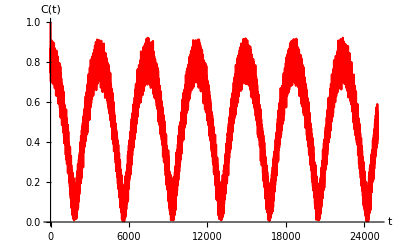

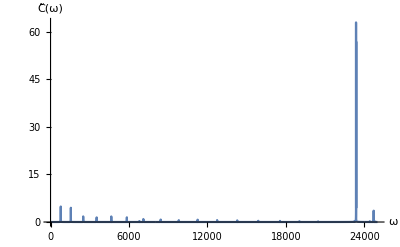

```mathematica
correl1=ListPlot[Abs[ct1],Joined->True,PlotStyle->RGBColor[1,0,0],AxesLabel->{"t","C(t)"}]
cft1=Fourier[ct];
ct1plot=ListPlot[Abs[cft1],PlotRange->All,Joined->True,AxesLabel->{"ω","\!\(\*OverscriptBox[\(C\), \(~\)]\)(ω)"}]
```

```mathematica
ListPlot[Transpose[{pts,-(ψ⟦1⟧+ψ⟦2⟧)/(√2)}],Joined->True]
ϕo=-(ψ⟦1⟧+ψ⟦2⟧)/(√2);
ψt={ϕo};
ct={1};
evolve={ListPlot[Transpose[{pts,ϕo}],Joined->True,DisplayFunction->Identity]};
nsteps=25000;
ϕt=ϕo;
Do[ϕt=U.ϕt;c=ϕo.ϕt;ct=Append[ct,c];If[Mod[n,10000]==0,ψt=Append[ψt,ϕt];pp=ListPlot[Transpose[{pts,Abs[ϕt]}],Joined->True,DisplayFunction->Identity];evolve=Append[evolve,pp]],{n,nsteps}];
ct2=ct;
```